```mathematica
example={P0x-> 0, P1x-> 1.5, P2x-> 1, P0y-> 0, P1y-> 0.5, P2y-> 0}
```

{P0x→0,P1x→1.5,P2x→1,P0y→0,P1y→0.5,P2y→0}

```mathematica
pts={P0,P1,P2}
```

{{P0x,P0y},{P1x,P1y},{P2x,P2y}}

```mathematica
f=BezierFunction[pts]
```

BezierFunction[{{P0x,P0y},{P1x,P1y},{P2x,P2y}}]

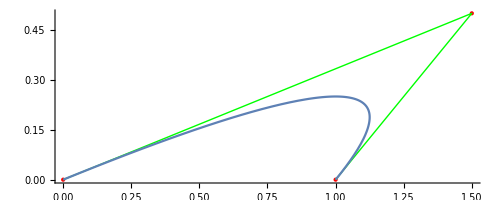

```mathematica
Show[Graphics[{Red,Point[pts],Green,Line[pts]},Axes->True],ParametricPlot[f[t]/.example,{t,0,1}]]/.example
```

```mathematica
D[f,{P1x}]
```

BezierFunction^({{0,0},{1,0},{0,0}})[{{P0x,P0y},{P1x,P1y},{P2x,P2y}}]

```mathematica
1/(P1x^2+P1y^2)
```

1/(P1x^2+P1y^2)

```mathematica
Plot3D[1/(P1x^2+P1y^2),{P1x,-10.,10.},{P1y,-10.,10.}]
```

-Graphics3D-

```mathematica
f
```

BezierFunction[{{P0x,P0y},{P1x,P1y},{P2x,P2y}}]